```mathematica
Clear[a,b,c];
list =Join[Table[a,{x,10}],Table[b+(-b+c)Mod[y,2],{y,10}]];
WheelGraph[11,EdgeWeight-> list];
Normal[WeightedAdjacencyMatrix[%]];
```

```mathematica
z;
```

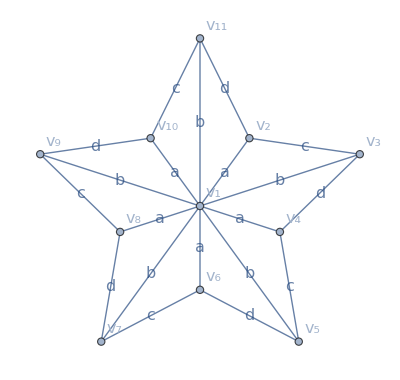

{11,1}

Σ = (5 a+5 b | -a | -b | -a | -b | -a | -b | -a | -b | -a | -b
-a | a+c+d | -c | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -d
-b | -c | b+c+d | -d | 0 | 0 | 0 | 0 | 0 | 0 | 0
-a | 0 | -d | a+c+d | -c | 0 | 0 | 0 | 0 | 0 | 0
-b | 0 | 0 | -c | b+c+d | -d | 0 | 0 | 0 | 0 | 0
-a | 0 | 0 | 0 | -d | a+c+d | -c | 0 | 0 | 0 | 0
-b | 0 | 0 | 0 | 0 | -c | b+c+d | -d | 0 | 0 | 0
-a | 0 | 0 | 0 | 0 | 0 | -d | a+c+d | -c | 0 | 0
-b | 0 | 0 | 0 | 0 | 0 | 0 | -c | b+c+d | -d | 0
-a | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -d | a+c+d | -c
-b | -d | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -c | b+c+d)

Σ' = (a+c+d | -c | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -d
-c | b+c+d | -d | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -d | a+c+d | -c | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -c | b+c+d | -d | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -d | a+c+d | -c | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -c | b+c+d | -d | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -d | a+c+d | -c | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -c | b+c+d | -d | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -d | a+c+d | -c
-d | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -c | b+c+d)

Σ'' = (a+c+d | -c | 0 | 0 | 0 | 0 | 0 | 0 | 0
-c | b+c+d | -d | 0 | 0 | 0 | 0 | 0 | 0
0 | -d | a+c+d | -c | 0 | 0 | 0 | 0 | 0
0 | 0 | -c | b+c+d | -d | 0 | 0 | 0 | 0
0 | 0 | 0 | -d | a+c+d | -c | 0 | 0 | 0
0 | 0 | 0 | 0 | -c | b+c+d | -d | 0 | 0
0 | 0 | 0 | 0 | 0 | -d | a+c+d | -c | 0
0 | 0 | 0 | 0 | 0 | 0 | -c | b+c+d | -d
0 | 0 | 0 | 0 | 0 | 0 | 0 | -d | a+c+d)

R_eq = Det[(a+c+d | -c | 0 | 0 | 0 | 0 | 0 | 0 | 0
-c | b+c+d | -d | 0 | 0 | 0 | 0 | 0 | 0
0 | -d | a+c+d | -c | 0 | 0 | 0 | 0 | 0
0 | 0 | -c | b+c+d | -d | 0 | 0 | 0 | 0
0 | 0 | 0 | -d | a+c+d | -c | 0 | 0 | 0
0 | 0 | 0 | 0 | -c | b+c+d | -d | 0 | 0
0 | 0 | 0 | 0 | 0 | -d | a+c+d | -c | 0
0 | 0 | 0 | 0 | 0 | 0 | -c | b+c+d | -d
0 | 0 | 0 | 0 | 0 | 0 | 0 | -d | a+c+d)]/Det[(a+c+d | -c | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -d
-c | b+c+d | -d | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -d | a+c+d | -c | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -c | b+c+d | -d | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -d | a+c+d | -c | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -c | b+c+d | -d | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -d | a+c+d | -c | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -c | b+c+d | -d | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -d | a+c+d | -c
-d | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -c | b+c+d)]

R_eq = ((-d^2 (-d^2 (-d^2 (-d^2 (a+c+d)+(a+c+d) (-c^2+(a+c+d) (b+c+d)))+(a+c+d) (-c^2 (-c^2+(a+c+d) (b+c+d))+(b+c+d) (-d^2 (a+c+d)+(a+c+d) (-c^2+(a+c+d) (b+c+d)))))+(a+c+d) (-c^2 (-c^2 (-c^2+(a+c+d) (b+c+d))+(b+c+d) (-d^2 (a+c+d)+(a+c+d) (-c^2+(a+c+d) (b+c+d))))+(b+c+d) (-d^2 (-d^2 (a+c+d)+(a+c+d) (-c^2+(a+c+d) (b+c+d)))+(a+c+d) (-c^2 (-c^2+(a+c+d) (b+c+d))+(b+c+d) (-d^2 (a+c+d)+(a+c+d) (-c^2+(a+c+d) (b+c+d)))))))+(a+c+d) (-c^2 (-c^2 (-c^2 (-c^2+(a+c+d) (b+c+d))+(b+c+d) (-d^2 (a+c+d)+(a+c+d) (-c^2+(a+c+d) (b+c+d))))+(b+c+d) (-d^2 (-d^2 (a+c+d)+(a+c+d) (-c^2+(a+c+d) (b+c+d)))+(a+c+d) (-c^2 (-c^2+(a+c+d) (b+c+d))+(b+c+d) (-d^2 (a+c+d)+(a+c+d) (-c^2+(a+c+d) (b+c+d))))))+(b+c+d) (-d^2 (-d^2 (-d^2 (a+c+d)+(a+c+d) (-c^2+(a+c+d) (b+c+d)))+(a+c+d) (-c^2 (-c^2+(a+c+d) (b+c+d))+(b+c+d) (-d^2 (a+c+d)+(a+c+d) (-c^2+(a+c+d) (b+c+d)))))+(a+c+d) (-c^2 (-c^2 (-c^2+(a+c+d) (b+c+d))+(b+c+d) (-d^2 (a+c+d)+(a+c+d) (-c^2+(a+c+d) (b+c+d))))+(b+c+d) (-d^2 (-d^2 (a+c+d)+(a+c+d) (-c^2+(a+c+d) (b+c+d)))+(a+c+d) (-c^2 (-c^2+(a+c+d) (b+c+d))+(b+c+d) (-d^2 (a+c+d)+(a+c+d) (-c^2+(a+c+d) (b+c+d)))))))))/(c (-c^4 d^5-c (-c^2 (-c^2 (-c^2 (-c^2+(a+c+d) (b+c+d))+(b+c+d) (-d^2 (a+c+d)+(a+c+d) (-c^2+(a+c+d) (b+c+d))))+(b+c+d) (-d^2 (-d^2 (a+c+d)+(a+c+d) (-c^2+(a+c+d) (b+c+d)))+(a+c+d) (-c^2 (-c^2+(a+c+d) (b+c+d))+(b+c+d) (-d^2 (a+c+d)+(a+c+d) (-c^2+(a+c+d) (b+c+d))))))+(b+c+d) (-d^2 (-d^2 (-d^2 (a+c+d)+(a+c+d) (-c^2+(a+c+d) (b+c+d)))+(a+c+d) (-c^2 (-c^2+(a+c+d) (b+c+d))+(b+c+d) (-d^2 (a+c+d)+(a+c+d) (-c^2+(a+c+d) (b+c+d)))))+(a+c+d) (-c^2 (-c^2 (-c^2+(a+c+d) (b+c+d))+(b+c+d) (-d^2 (a+c+d)+(a+c+d) (-c^2+(a+c+d) (b+c+d))))+(b+c+d) (-d^2 (-d^2 (a+c+d)+(a+c+d) (-c^2+(a+c+d) (b+c+d)))+(a+c+d) (-c^2 (-c^2+(a+c+d) (b+c+d))+(b+c+d) (-d^2 (a+c+d)+(a+c+d) (-c^2+(a+c+d) (b+c+d)))))))))+(b+c+d) (-d^2 (-d^2 (-d^2 (-d^2 (a+c+d)+(a+c+d) (-c^2+(a+c+d) (b+c+d)))+(a+c+d) (-c^2 (-c^2+(a+c+d) (b+c+d))+(b+c+d) (-d^2 (a+c+d)+(a+c+d) (-c^2+(a+c+d) (b+c+d)))))+(a+c+d) (-c^2 (-c^2 (-c^2+(a+c+d) (b+c+d))+(b+c+d) (-d^2 (a+c+d)+(a+c+d) (-c^2+(a+c+d) (b+c+d))))+(b+c+d) (-d^2 (-d^2 (a+c+d)+(a+c+d) (-c^2+(a+c+d) (b+c+d)))+(a+c+d) (-c^2 (-c^2+(a+c+d) (b+c+d))+(b+c+d) (-d^2 (a+c+d)+(a+c+d) (-c^2+(a+c+d) (b+c+d)))))))+(a+c+d) (-c^2 (-c^2 (-c^2 (-c^2+(a+c+d) (b+c+d))+(b+c+d) (-d^2 (a+c+d)+(a+c+d) (-c^2+(a+c+d) (b+c+d))))+(b+c+d) (-d^2 (-d^2 (a+c+d)+(a+c+d) (-c^2+(a+c+d) (b+c+d)))+(a+c+d) (-c^2 (-c^2+(a+c+d) (b+c+d))+(b+c+d) (-d^2 (a+c+d)+(a+c+d) (-c^2+(a+c+d) (b+c+d))))))+(b+c+d) (-d^2 (-d^2 (-d^2 (a+c+d)+(a+c+d) (-c^2+(a+c+d) (b+c+d)))+(a+c+d) (-c^2 (-c^2+(a+c+d) (b+c+d))+(b+c+d) (-d^2 (a+c+d)+(a+c+d) (-c^2+(a+c+d) (b+c+d)))))+(a+c+d) (-c^2 (-c^2 (-c^2+(a+c+d) (b+c+d))+(b+c+d) (-d^2 (a+c+d)+(a+c+d) (-c^2+(a+c+d) (b+c+d))))+(b+c+d) (-d^2 (-d^2 (a+c+d)+(a+c+d) (-c^2+(a+c+d) (b+c+d)))+(a+c+d) (-c^2 (-c^2+(a+c+d) (b+c+d))+(b+c+d) (-d^2 (a+c+d)+(a+c+d) (-c^2+(a+c+d) (b+c+d)))))))))+d (-c^5 d^4-d (-d^2 (-d^2 (-d^2 (-d^2+(a+c+d) (b+c+d))+(a+c+d) (-c^2 (b+c+d)+(b+c+d) (-d^2+(a+c+d) (b+c+d))))+(a+c+d) (-c^2 (-c^2 (b+c+d)+(b+c+d) (-d^2+(a+c+d) (b+c+d)))+(b+c+d) (-d^2 (-d^2+(a+c+d) (b+c+d))+(a+c+d) (-c^2 (b+c+d)+(b+c+d) (-d^2+(a+c+d) (b+c+d))))))+(a+c+d) (-c^2 (-c^2 (-c^2 (b+c+d)+(b+c+d) (-d^2+(a+c+d) (b+c+d)))+(b+c+d) (-d^2 (-d^2+(a+c+d) (b+c+d))+(a+c+d) (-c^2 (b+c+d)+(b+c+d) (-d^2+(a+c+d) (b+c+d)))))+(b+c+d) (-d^2 (-d^2 (-d^2+(a+c+d) (b+c+d))+(a+c+d) (-c^2 (b+c+d)+(b+c+d) (-d^2+(a+c+d) (b+c+d))))+(a+c+d) (-c^2 (-c^2 (b+c+d)+(b+c+d) (-d^2+(a+c+d) (b+c+d)))+(b+c+d) (-d^2 (-d^2+(a+c+d) (b+c+d))+(a+c+d) (-c^2 (b+c+d)+(b+c+d) (-d^2+(a+c+d) (b+c+d)))))))))))

```mathematica
n = 5;
{Subscript[n, 1],Subscript[n, 2]} = {1,11};
Clear[a,b,c,d]
(*{a,b,c,d} = {1,1,1,1}*)


p = 2*n+1;


Table[1<->i,{i,2,2*n+1}];
Join[%,Table[i<->i+1,{i,2,2*n}]];
edges = Append[%,p<->2];


angles = Table[i*360/(2*n)*Pi/180, {i,2*n}];
coords = Table[{Sin[angles[[i]]]/(1+Mod[i,2]),Cos[angles[[i]]]/(1+Mod[i,2])},{i,Length[angles]}];
coords = Prepend[coords,{0,0}];

list = Join[Table[a+(-a+b)*Mod[x+1,2],{x,2*n}],Table[c+(-c+d)Mod[y+1,2],{y,2*n}]];
Graph[edges,VertexLabels->Table[i-> Style[Subscript[v, i],16],{i,p}],EdgeWeight-> list,EdgeLabels->Table[edges[[f]]-> Style[list[[f]],16],{f,Length[list]}],VertexCoordinates->coords]

sigma = Graph[edges,EdgeWeight-> list];
sigma = -Normal[WeightedAdjacencyMatrix[sigma]];

{Subscript[n, 1],Subscript[n, 2]} = Length[sigma]+1-{Subscript[n, 1],Subscript[n, 2]}

For[i=1,i≤ Length[sigma],i++, sum =0;
For[j =1, j≤Length[sigma],j++,sum =sum+ sigma[[i,j]]];
sigma[[i,i]] = -sum
];

Print[""]
Print[Style["Σ = ",24,Italic],Style[sigma//MatrixForm,18,Italic]]

sigmaprime = Minors[sigma,Length[sigma]-1,Identity][[Subscript[n, 1],Subscript[n, 1]]];
Print[""]
Print[Style["Σ' = ",24,Italic],Style[sigmaprime//MatrixForm,18,Italic]]

sigma2prime = Minors[sigmaprime,Length[sigma]-2,Identity][[Subscript[n, 2],Subscript[n, 2]]];
Print[""]
Print[Style["Σ'' = ",24,Italic],Style[sigma2prime//MatrixForm,18,Italic]]



ans = Det[sigma2prime//MatrixForm]/Det[sigmaprime//MatrixForm];
Print[""]
Print[Style["R_eq = ",24,Italic],Style[ans,18,Italic]]

Print[""]
Print[Style["R_eq = ",28,Italic],Style[Det[sigma2prime]/Det[sigmaprime],28,Italic]]
```